```mathematica
Zadanie 1
```

```mathematica
SetDirectory["/dmj/2000/mzpos/_work_/mathematica"]
```

/work/2000/mzpos/mathematica

```mathematica
FileNames["*","/work/2000/mzpos/mathematica"]
```

{/work/2000/mzpos/mathematica/prackomp.html,/work/2000/mzpos/mathematica/Z3_data.dat}

```mathematica
"/work/2000/mzpos/mathematica/Z3_data.dat"
```

/work/2000/mzpos/mathematica/Z3_data.dat

```mathematica
Dane=Import["Z3_data.dat","Table"]
```

{{-0.09,-0.06608},{-0.08,-0.05885},{-0.07,0.11019},{-0.06,0.11501},{-0.05,0.1199},{-0.04,-0.02969},{-0.03,-0.02232},{-0.02,-0.01492},{-0.01,-0.00748},{0,0},{0.01,0.00752},{0.02,0.01508},{0.03,0.02269},{0.04,0.03034},{0.05,0.03803},{0.06,-0.06097},{0.07,0.11019},{0.08,0.11713},{0.09,0.06924},{0.1,-0.04777},{0.11,-0.03793},{0.12,-0.0281},{0.13,0.04181},{0.14,0.0508},{0.15,0.05982},{0.16,0.1255},{0.17,0.13369},{0.18,0.14192},{0.19,0.13882},{0.2,0.14728},{0.21,-0.04007},{0.22,-0.0286},{0.23,0.14465},{0.24,0.15363},{0.25,0.16263},{0.26,0.01709},{0.27,0.02845},{0.28,0.03978},{0.29,0.05107},{0.3,0.06233},{0.31,0.07354},{0.32,0.0847},{0.33,0.09581},{0.34,0.10687},{0.35,0.11787},{0.36,0.02207},{0.37,0.19632},{0.38,0.20624},{0.39,0.1612},{0.4,0.04691},{0.41,0.05934},{0.42,0.07164},{0.43,0.14387},{0.44,0.15504},{0.45,0.1661},{0.46,0.23367},{0.47,0.2436},{0.48,0.25341},{0.49,0.24592},{0.5,0.25574},{0.51,0.21053},{0.52,0.096},{0.53,0.1081},{0.54,0.12001},{0.55,0.19176},{0.56,0.20239},{0.57,0.21282},{0.58,0.2797},{0.59,0.28886},{0.6,0.29781},{0.61,0.29522},{0.62,0.30395},{0.63,0.11663},{0.64,0.12789},{0.65,0.30069},{0.66,0.30899},{0.67,0.31705},{0.68,0.17034},{0.69,0.18027},{0.7,0.18993},{0.71,0.19931},{0.72,0.2084},{0.73,0.21721},{0.74,0.22572},{0.75,0.23394},{0.76,0.24186},{0.77,0.24948},{0.78,0.15007},{0.79,0.32045},{0.8,0.32628},{0.81,0.27691},{0.82,0.15806},{0.83,0.1657},{0.84,0.17299},{0.85,0.23998},{0.86,0.24571},{0.87,0.2511},{0.88,0.31279},{0.89,0.31083},{0.9,0.31444},{0.91,0.26284},{0.92,0.14174},{0.93,0.1471},{0.94,0.15209},{0.95,0.21677},{0.96,0.22017},{0.97,0.22322},{0.98,0.28257},{0.99,0.28406},{1,0.28523},{1.01,0.27471},{1.02,0.2754},{1.03,0.07993},{1.04,0.08294},{1.05,0.24739},{1.06,0.24725},{1.07,0.24679},{1.08,0.09149},{1.09,0.09276},{1.1,0.09371},{1.11,0.09432},{1.12,0.09461},{1.13,0.09458},{1.14,0.09423},{1.15,0.09357},{1.16,0.09261},{1.17,0.09135},{1.18,-0.01694},{1.19,0.1446},{1.2,0.14159},{1.21,0.08344},{1.22,-0.04415},{1.23,-0.04519},{1.24,-0.04653},{1.25,0.01192},{1.26,0.00917},{1.27,0.00618},{1.28,0.0596},{1.29,0.05528},{1.3,0.05075},{1.31,0.02886},{1.32,0.02421},{1.33,-0.03551},{1.34,-0.16457},{1.35,-0.16702},{1.36,-0.16966},{1.37,-0.11244},{1.38,-0.11632},{1.39,-0.12035},{1.4,-0.06788},{1.41,-0.07305},{1.42,-0.07834},{1.43,-0.09507},{1.44,-0.10036},{1.45,-0.30157},{1.46,-0.30405},{1.47,-0.14483},{1.48,-0.14993},{1.49,-0.15508},{1.5,-0.3148},{1.51,-0.31764},{1.52,-0.32052},{1.53,-0.32343},{1.54,-0.32636},{1.55,-0.3293},{1.56,-0.33224},{1.57,-0.33516},{1.58,-0.33806},{1.59,-0.34092},{1.6,-0.45048},{1.61,-0.28986},{1.62,-0.29344},{1.63,-0.35181},{1.64,-0.47926},{1.65,-0.47982},{1.66,-0.4803},{1.67,-0.42064},{1.68,-0.4218},{1.69,-0.42283},{1.7,-0.36708},{1.71,-0.36871},{1.72,-0.37016},{1.73,-0.51029},{1.74,-0.50925},{1.75,-0.50804},{1.76,-0.50666},{1.77,-0.50508},{1.78,-0.5033},{1.79,-0.50132},{1.8,-0.49912},{1.81,-0.60343},{1.82,-0.4374},{1.83,-0.43539},{1.84,-0.48801},{1.85,-0.60954},{1.86,-0.604},{1.87,-0.59824},{1.88,-0.53218},{1.89,-0.52679},{1.9,-0.52112},{1.91,-0.45853},{1.92,-0.45318},{1.93,-0.44752},{1.94,-0.45871},{1.95,-0.45215},{1.96,-0.50018},{1.97,-0.61705},{1.98,-0.60682},{1.99,-0.5963},{2,-0.52545},{2.01,-0.51522},{2.02,-0.50468},{2.03,-0.43719},{2.04,-0.42689},{2.05,-0.41627},{2.06,-0.41666},{2.07,-0.40519},{2.08,-0.58923},{2.09,-0.57414},{2.1,-0.39695},{2.11,-0.38371},{2.12,-0.37014},{2.13,-0.51078},{2.14,-0.49421},{2.15,-0.47734},{2.16,-0.46018},{2.17,-0.44273},{2.18,-0.42499},{2.19,-0.40697},{2.2,-0.38867},{2.21,-0.37009},{2.22,-0.35124},{2.23,-0.43885},{2.24,-0.25609},{2.25,-0.23732},{2.26,-0.27318},{2.27,-0.37795},{2.28,-0.35568},{2.29,-0.33321},{2.3,-0.25048},{2.31,-0.22848},{2.32,-0.20628},{2.33,-0.12723},{2.34,-0.10551},{2.35,-0.0836},{2.36,-0.25735},{2.37,-0.23211},{2.38,-0.04494},{2.39,-0.02189},{2.4,0.0013},{2.41,-0.12991},{2.42,-0.10409},{2.43,-0.07819},{2.44,-0.05221},{2.45,-0.02616},{2.46,-0.0000537197},{2.47,0.0261},{2.48,0.05228},{2.49,0.07849},{2.5,0.10471},{2.51,0.02419},{2.52,0.21378},{2.53,0.23908},{2.54,0.20947},{2.55,0.11065},{2.56,0.13857},{2.57,0.16638},{2.58,0.25412},{2.59,0.28082},{2.6,0.3074},{2.61,0.39048},{2.62,0.4159},{2.63,0.44117},{2.64,0.45492},{2.65,0.48003},{2.66,0.30911},{2.67,0.33678},{2.68,0.526},{2.69,0.55071},{2.7,0.57517},{2.71,0.44484},{2.72,0.47112},{2.73,0.49709},{2.74,0.52272},{2.75,0.54802},{2.76,0.57295},{2.77,0.59752},{2.78,0.62171},{2.79,0.6455},{2.8,0.66889},{2.81,0.58512},{2.82,0.77104},{2.83,0.79225},{2.84,0.75813},{2.85,0.65438},{2.86,0.67695},{2.87,0.699},{2.88,0.78057},{2.89,0.80068},{2.9,0.82025},{2.91,0.89592},{2.92,0.91352},{2.93,0.93056},{2.94,0.92988},{2.95,0.94606},{2.96,0.90677},{2.97,0.7977},{2.98,0.81483},{2.99,0.83129},{3,0.90715},{3.01,0.92143},{3.02,0.93504},{3.03,1.00464},{3.04,1.01604},{3.05,1.02678},{3.06,1.02551},{3.07,1.03508},{3.08,0.84813},{3.09,0.8593},{3.1,1.03153},{3.11,1.0388},{3.12,1.04535},{3.13,0.89666},{3.14,0.90416},{3.15,0.91092},{3.16,0.91692},{3.17,0.92219},{3.18,0.92671},{3.19,0.93048},{3.2,0.9335},{3.21,0.93577},{3.22,0.9373},{3.23,0.83135},{3.24,0.99477},{3.25,0.99319},{3.26,0.93599},{3.27,0.80889},{3.28,0.80786},{3.29,0.80606},{3.3,0.86356},{3.31,0.85939},{3.32,0.8545},{3.33,0.90553},{3.34,0.89251},{3.35,0.8847},{3.36,0.8213},{3.37,0.68806},{3.38,0.68092},{3.39,0.67308},{3.4,0.72458},{3.41,0.71448},{3.42,0.70372},{3.43,0.74895},{3.44,0.73602},{3.45,0.72247},{3.46,0.69697},{3.47,0.6824},{3.48,0.47141},{3.49,0.45865},{3.5,0.60709},{3.51,0.59071},{3.52,0.57379},{3.53,0.40182},{3.54,0.38623},{3.55,0.37012},{3.56,0.35351},{3.57,0.33641},{3.58,0.31883},{3.59,0.30079},{3.6,0.28232},{3.61,0.26342},{3.62,0.24411},{3.63,0.11768},{3.64,0.26099},{3.65,0.23969},{3.66,0.16317},{3.67,0.01718},{3.68,-0.00232},{3.69,-0.02212},{3.7,0.01783},{3.71,-0.0034},{3.72,-0.02487},{3.73,0.0101},{3.74,-0.01265},{3.75,-0.03555},{3.76,-0.07576},{3.77,-0.09865},{3.78,-0.17654},{3.79,-0.32368},{3.8,-0.3441},{3.81,-0.3646},{3.82,-0.3251},{3.83,-0.34657},{3.84,-0.36804},{3.85,-0.33284},{3.86,-0.35512},{3.87,-0.37733},{3.88,-0.41079},{3.89,-0.4326},{3.9,-0.65012},{3.91,-0.66867},{3.92,-0.52529},{3.93,-0.54599},{3.94,-0.56648},{3.95,-0.74127},{3.96,-0.75891},{3.97,-0.7763},{3.98,-0.79343},{3.99,-0.81028},{4,-0.82682},{4.01,-0.84303},{4.02,-0.8589},{4.03,-0.87441},{4.04,-0.88954},{4.05,-1.011},{4.06,-0.86193},{4.07,-0.87669},{4.08,-0.94587},{4.09,-1.08374},{4.1,-1.09432},{4.11,-1.10443},{4.12,-1.054},{4.13,-1.06398},{4.14,-1.07342},{4.15,-1.02566},{4.16,-1.03485},{4.17,-1.04344},{4.18,-1.19027},{4.19,-1.19549},{4.2,-1.2001},{4.21,-1.20409},{4.22,-1.20744},{4.23,-1.21013},{4.24,-1.21217},{4.25,-1.21353},{4.26,-1.32094},{4.27,-1.15755},{4.28,-1.15771},{4.29,-1.21205},{4.3,-1.33482},{4.31,-1.33007},{4.32,-1.32462},{4.33,-1.2584},{4.34,-1.25239},{4.35,-1.24564},{4.36,-1.18149},{4.37,-1.17412},{4.38,-1.16598},{4.39,-1.17423},{4.4,-1.16427},{4.41,-1.20843},{4.42,-1.321},{4.43,-1.30599},{4.44,-1.29027},{4.45,-1.21375},{4.46,-1.19742},{4.47,-1.18034},{4.48,-1.10587},{4.49,-1.08818},{4.5,-1.06973},{4.51,-1.06188},{4.52,-1.04175},{4.53,-1.21673},{4.54,-1.19216},{4.55,-1.00511},{4.56,-0.98162},{4.57,-0.95741},{4.58,-1.08705},{4.59,-1.05909},{4.6,-1.03048},{4.61,-1.00122},{4.62,-0.97133},{4.63,-0.94081},{4.64,-0.90969},{4.65,-0.87795},{4.66,-0.84563},{4.67,-0.81273},{4.68,-0.88601},{4.69,-0.68862},{4.7,-0.65495},{4.71,-0.67564},{4.72,-0.76499},{4.73,-0.72705},{4.74,-0.68867},{4.75,-0.58982},{4.76,-0.55147},{4.77,-0.51271},{4.78,-0.41692},{4.79,-0.37828},{4.8,-0.33926},{4.81,-0.49574},{4.82,-0.45309},{4.83,-0.24838},{4.84,-0.20764},{4.85,-0.16665},{4.86,-0.27996},{4.87,-0.23614},{4.88,-0.19216},{4.89,-0.14803},{4.9,-0.10378},{4.91,-0.05942},{4.92,-0.01499},{4.93,0.02951},{4.94,0.07404},{4.95,0.11858},{4.96,0.05638},{4.97,0.26425},{4.98,0.3078},{4.99,0.2964},{5,0.21572},{5.01,0.26171},{5.02,0.30751},{5.03,0.41316},{5.04,0.45765},{5.05,0.5019},{5.06,0.60253},{5.07,0.64536},{5.08,0.68788},{5.09,0.71873},{5.1,0.76076},{5.11,0.60658},{5.12,0.6508},{5.13,0.85636},{5.14,0.89719},{5.15,0.93755},{5.16,0.82288},{5.17,0.86458},{5.18,0.90571},{5.19,0.94624},{5.2,0.98616},{5.21,1.02543},{5.22,1.06405},{5.23,1.10197},{5.24,1.1392},{5.25,1.17569},{5.26,1.10471},{5.27,1.30307},{5.28,1.33639},{5.29,1.31402},{5.3,1.22166},{5.31,1.25525},{5.32,1.28795},{5.33,1.37979},{5.34,1.40978},{5.35,1.43884},{5.36,1.5236},{5.37,1.54988},{5.38,1.5752},{5.39,1.58237},{5.4,1.60599},{5.41,1.57371},{5.42,1.47122},{5.43,1.4945},{5.44,1.51667},{5.45,1.5978},{5.46,1.61689},{5.47,1.63488},{5.48,1.7084},{5.49,1.72328},{5.5,1.73703},{5.51,1.73831},{5.52,1.74999},{5.53,1.56468},{5.54,1.57703},{5.55,1.74998},{5.56,1.7575},{5.57,1.76385},{5.58,1.61449},{5.59,1.62086},{5.6,1.62602},{5.61,1.62998},{5.62,1.63274},{5.63,1.63429},{5.64,1.63465},{5.65,1.6338},{5.66,1.63176},{5.67,1.62852},{5.68,1.51736},{5.69,1.67513},{5.7,1.66747},{5.71,1.60375},{5.72,1.46971},{5.73,1.46131},{5.74,1.45173},{5.75,1.50104},{5.76,1.48826},{5.77,1.47436},{5.78,1.51598},{5.79,1.49317},{5.8,1.47518},{5.81,1.40123},{5.82,1.25705},{5.83,1.23863},{5.84,1.21913},{5.85,1.25865},{5.86,1.23621},{5.87,1.21278},{5.88,1.24502},{5.89,1.21878},{5.9,1.19162},{5.91,1.1522},{5.92,1.12343},{5.93,0.89795},{5.94,0.87044},{5.95,1.00386},{5.96,0.97221},{5.97,0.93979},{5.98,0.75207},{5.99,0.72052},{6,0.68824},{6.01,0.65525},{6.02,0.62159},{6.03,0.58726},{6.04,0.55231},{6.05,0.51677},{6.06,0.48065},{6.07,0.44399},{6.08,0.30008},{6.09,0.42579},{6.1,0.3868},{6.11,0.2925},{6.12,0.12864},{6.13,0.09122},{6.14,0.05343},{6.15,0.07535},{6.16,0.03605},{6.17,-0.0035},{6.18,0.01338},{6.19,-0.02746},{6.2,-0.06845},{6.21,-0.12671},{6.22,-0.16762},{6.23,-0.26347},{6.24,-0.42852},{6.25,-0.46677},{6.26,-0.50503},{6.27,-0.48319},{6.28,-0.52221},{6.29,-0.56111},{6.3,-0.54323},{6.31,-0.58267},{6.32,-0.6219},{6.33,-0.67221},{6.34,-0.71071},{6.35,-0.94473},{6.36,-0.9796},{6.37,-0.85233},{6.38,-0.88892},{6.39,-0.92507},{6.4,-1.11529},{6.41,-1.14812},{6.42,-1.18045},{6.43,-1.21225},{6.44,-1.2435},{6.45,-1.27415},{6.46,-1.30419},{6.47,-1.33359},{6.48,-1.36232},{6.49,-1.39035},{6.5,-1.52439},{6.51,-1.38756},{6.52,-1.41422},{6.53,-1.49495},{6.54,-1.64402},{6.55,-1.66544},{6.56,-1.68602},{6.57,-1.64568},{6.58,-1.66537},{6.59,-1.68413},{6.6,-1.64529},{6.61,-1.663},{6.62,-1.67971},{6.63,-1.83425},{6.64,-1.84676},{6.65,-1.85825},{6.66,-1.86868},{6.67,-1.87804},{6.68,-1.88632},{6.69,-1.89351},{6.7,-1.89958},{6.71,-2.01126},{6.72,-1.8517},{6.73,-1.85524},{6.74,-1.9125},{6.75,-2.03775},{6.76,-2.03502},{6.77,-2.03114},{6.78,-1.96605},{6.79,-1.9607},{6.8,-1.95415},{6.81,-1.88976},{6.82,-1.88168},{6.83,-1.87238},{6.84,-1.87902},{6.85,-1.867},{6.86,-1.90865},{6.87,-2.01825},{6.88,-1.99984},{6.89,-1.98025},{6.9,-1.89944},{6.91,-1.87838},{6.92,-1.85613},{6.93,-1.77605},{6.94,-1.75232},{6.95,-1.72741},{6.96,-1.71268},{6.97,-1.68526},{6.98,-1.85252},{6.99,-1.81984},{7,-1.62428},{7.01,-1.59187},{7.02,-1.55837},{7.03,-1.67832},{7.04,-1.6403},{7.05,-1.60125},{7.06,-1.5612},{7.07,-1.52016},{7.08,-1.47814},{7.09,-1.43517},{7.1,-1.39126},{7.11,-1.34643},{7.12,-1.30071},{7.13,-1.36085},{7.14,-1.15003},{7.15,-1.10263},{7.16,-1.10932},{7.17,-1.18438},{7.18,-1.13189},{7.19,-1.0787},{7.2,-0.96479},{7.21,-0.91116},{7.22,-0.85689},{7.23,-0.74536},{7.24,-0.69077},{7.25,-0.63563},{7.26,-0.77579},{7.27,-0.71664},{7.28,-0.49526},{7.29,-0.43771},{7.3,-0.37976},{7.31,-0.47598},{7.32,-0.41495},{7.33,-0.35365},{7.34,-0.2921},{7.35,-0.23034},{7.36,-0.1684},{7.37,-0.10631},{7.38,-0.04412},{7.39,0.01816},{7.4,0.08048},{7.41,0.03606},{7.42,0.26174},{7.43,0.32309},{7.44,0.32947},{7.45,0.26655},{7.46,0.33026},{7.47,0.39373},{7.48,0.51699},{7.49,0.57901},{7.5,0.64072},{7.51,0.75871},{7.52,0.81879},{7.53,0.87845},{7.54,0.92631},{7.55,0.98522},{7.56,0.84776},{7.57,0.90854},{7.58,1.13049},{7.59,1.18754},{7.6,1.24392},{7.61,1.14507},{7.62,1.20237},{7.63,1.25889},{7.64,1.31457},{7.65,1.3694},{7.66,1.42334},{7.67,1.47635},{7.68,1.52841},{7.69,1.57949},{7.7,1.62956},{7.71,1.57184},{7.72,1.78317},{7.73,1.82914},{7.74,1.81911},{7.75,1.73876},{7.76,1.78402},{7.77,1.82805},{7.78,1.93086},{7.79,1.97147},{7.8,2.01079},{7.81,2.10544},{7.82,2.14123},{7.83,2.17567},{7.84,2.19158},{7.85,2.22355},{7.86,2.19921},{7.87,2.10426},{7.88,2.13467},{7.89,2.16356},{7.9,2.25099},{7.91,2.27596},{7.92,2.29941},{7.93,2.37795},{7.94,2.39742},{7.95,2.41534},{7.96,2.42034},{7.97,2.4353},{7.98,2.25283},{7.99,2.26758},{8,2.44248},{8.01,2.45151},{8.02,2.45893},{8.03,2.31019},{8.04,2.31673},{8.05,2.32161},{8.06,2.32485},{8.07,2.32644},{8.08,2.32638},{8.09,2.32467},{8.1,2.32133},{8.11,2.31634},{8.12,2.30973},{8.13,2.19475},{8.14,2.34827},{8.15,2.33593},{8.16,2.2671},{8.17,2.12753},{8.18,2.11318},{8.19,2.09723},{8.2,2.13975},{8.21,2.11978},{8.22,2.09829},{8.23,2.13192},{8.24,2.10072},{8.25,2.07396},{8.26,1.99085},{8.27,1.83715},{8.28,1.80883},{8.29,1.77908},{8.3,1.80797},{8.31,1.77457},{8.32,1.73983},{8.33,1.76043},{8.34,1.72222},{8.35,1.68277},{8.36,1.63075},{8.37,1.58907},{8.38,1.3504},{8.39,1.3094},{8.4,1.42907},{8.41,1.38339},{8.42,1.33668},{8.43,1.13442},{8.44,1.0881},{8.45,1.04081},{8.46,0.99259},{8.47,0.94348},{8.48,0.89351},{8.49,0.84273},{8.5,0.79116},{8.51,0.73886},{8.52,0.68585},{8.53,0.52544},{8.54,0.63453},{8.55,0.57877},{8.56,0.46759},{8.57,0.28675},{8.58,0.23224},{8.59,0.17728},{8.6,0.18196},{8.61,0.12536},{8.62,0.06846},{8.63,0.06794},{8.64,0.00968},{8.65,-0.04875},{8.66,-0.12446},{8.67,-0.18281},{8.68,-0.29609},{8.69,-0.47854},{8.7,-0.53415},{8.71,-0.58972},{8.72,-0.58513},{8.73,-0.64134},{8.74,-0.69733},{8.75,-0.69645},{8.76,-0.7528},{8.77,-0.8088},{8.78,-0.87578},{8.79,-0.9308},{8.8,-1.18119},{8.81,-1.23227},{8.82,-1.12105},{8.83,-1.17351},{8.84,-1.22534},{8.85,-1.43105},{8.86,-1.47915},{8.87,-1.52654},{8.88,-1.57317},{8.89,-1.619},{8.9,-1.664},{8.91,-1.70813},{8.92,-1.75136},{8.93,-1.79364},{8.94,-1.83494},{8.95,-1.98196},{8.96,-1.85781},{8.97,-1.89684},{8.98,-1.98964},{8.99,-2.15044},{9,-2.18327},{9.01,-2.21492},{9.02,-2.18531},{9.03,-2.21538},{9.04,-2.24416},{9.05,-2.21498},{9.06,-2.24198},{9.07,-2.26761},{9.08,-2.43067},{9.09,-2.45134},{9.1,-2.47057},{9.11,-2.48837},{9.12,-2.50469},{9.13,-2.51953},{9.14,-2.53286},{9.15,-2.54466},{9.16,-2.66166},{9.17,-2.50699},{9.18,-2.51501},{9.19,-2.57632},{9.2,-2.70519},{9.21,-2.70566},{9.22,-2.70454},{9.23,-2.64177},{9.24,-2.63832},{9.25,-2.63323},{9.26,-2.56985},{9.27,-2.56236},{9.28,-2.55321},{9.29,-2.55956},{9.3,-2.54681},{9.31,-2.5873},{9.32,-2.6953},{9.33,-2.67486},{9.34,-2.65281},{9.35,-2.5691},{9.36,-2.54472},{9.37,-2.51871},{9.38,-2.43446},{9.39,-2.40614},{9.4,-2.37622},{9.41,-2.35606},{9.42,-2.3228},{9.43,-2.48382},{9.44,-2.4445},{9.45,-2.24189},{9.46,-2.20204},{9.47,-2.16071},{9.48,-2.27245},{9.49,-2.22584},{9.5,-2.17784},{9.51,-2.12846},{9.52,-2.07773},{9.53,-2.02567},{9.54,-1.97231},{9.55,-1.91767},{9.56,-1.86178},{9.57,-1.80467},{9.58,-1.8531},{9.59,-1.63026},{9.6,-1.57054},{9.61,-1.56461},{9.62,-1.62677},{9.63,-1.56109},{9.64,-1.49445},{9.65,-1.36683},{9.66,-1.29923},{9.67,-1.23074},{9.68,-1.10477},{9.69,-1.03552},{9.7,-0.96549},{9.71,-0.91188},{9.72,-0.84014},{9.73,-0.82263},{9.74,-0.87368},{9.75,-0.79738},{9.76,-0.72058},{9.77,-0.58329},{9.78,-0.50652},{9.79,-0.42937},{9.8,-0.29524},{9.81,-0.21834},{9.82,-0.19608},{9.83,-0.24277},{9.84,-0.16251},{9.85,-0.08218},{9.86,0.05824},{9.87,0.13774},{9.88,0.21719},{9.89,0.3532},{9.9,0.43156}}

```mathematica
Dimensions[Dane]
```

{1000,2}

```mathematica
Dane[[All,1]]
```

{-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2,2.01,2.02,2.03,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.26,2.27,2.28,2.29,2.3,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.51,2.52,2.53,2.54,2.55,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.76,2.77,2.78,2.79,2.8,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3,3.01,3.02,3.03,3.04,3.05,3.06,3.07,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.26,3.27,3.28,3.29,3.3,3.31,3.32,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5,3.51,3.52,3.53,3.54,3.55,3.56,3.57,3.58,3.59,3.6,3.61,3.62,3.63,3.64,3.65,3.66,3.67,3.68,3.69,3.7,3.71,3.72,3.73,3.74,3.75,3.76,3.77,3.78,3.79,3.8,3.81,3.82,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9,3.91,3.92,3.93,3.94,3.95,3.96,3.97,3.98,3.99,4,4.01,4.02,4.03,4.04,4.05,4.06,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,4.22,4.23,4.24,4.25,4.26,4.27,4.28,4.29,4.3,4.31,4.32,4.33,4.34,4.35,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,4.5,4.51,4.52,4.53,4.54,4.55,4.56,4.57,4.58,4.59,4.6,4.61,4.62,4.63,4.64,4.65,4.66,4.67,4.68,4.69,4.7,4.71,4.72,4.73,4.74,4.75,4.76,4.77,4.78,4.79,4.8,4.81,4.82,4.83,4.84,4.85,4.86,4.87,4.88,4.89,4.9,4.91,4.92,4.93,4.94,4.95,4.96,4.97,4.98,4.99,5,5.01,5.02,5.03,5.04,5.05,5.06,5.07,5.08,5.09,5.1,5.11,5.12,5.13,5.14,5.15,5.16,5.17,5.18,5.19,5.2,5.21,5.22,5.23,5.24,5.25,5.26,5.27,5.28,5.29,5.3,5.31,5.32,5.33,5.34,5.35,5.36,5.37,5.38,5.39,5.4,5.41,5.42,5.43,5.44,5.45,5.46,5.47,5.48,5.49,5.5,5.51,5.52,5.53,5.54,5.55,5.56,5.57,5.58,5.59,5.6,5.61,5.62,5.63,5.64,5.65,5.66,5.67,5.68,5.69,5.7,5.71,5.72,5.73,5.74,5.75,5.76,5.77,5.78,5.79,5.8,5.81,5.82,5.83,5.84,5.85,5.86,5.87,5.88,5.89,5.9,5.91,5.92,5.93,5.94,5.95,5.96,5.97,5.98,5.99,6,6.01,6.02,6.03,6.04,6.05,6.06,6.07,6.08,6.09,6.1,6.11,6.12,6.13,6.14,6.15,6.16,6.17,6.18,6.19,6.2,6.21,6.22,6.23,6.24,6.25,6.26,6.27,6.28,6.29,6.3,6.31,6.32,6.33,6.34,6.35,6.36,6.37,6.38,6.39,6.4,6.41,6.42,6.43,6.44,6.45,6.46,6.47,6.48,6.49,6.5,6.51,6.52,6.53,6.54,6.55,6.56,6.57,6.58,6.59,6.6,6.61,6.62,6.63,6.64,6.65,6.66,6.67,6.68,6.69,6.7,6.71,6.72,6.73,6.74,6.75,6.76,6.77,6.78,6.79,6.8,6.81,6.82,6.83,6.84,6.85,6.86,6.87,6.88,6.89,6.9,6.91,6.92,6.93,6.94,6.95,6.96,6.97,6.98,6.99,7,7.01,7.02,7.03,7.04,7.05,7.06,7.07,7.08,7.09,7.1,7.11,7.12,7.13,7.14,7.15,7.16,7.17,7.18,7.19,7.2,7.21,7.22,7.23,7.24,7.25,7.26,7.27,7.28,7.29,7.3,7.31,7.32,7.33,7.34,7.35,7.36,7.37,7.38,7.39,7.4,7.41,7.42,7.43,7.44,7.45,7.46,7.47,7.48,7.49,7.5,7.51,7.52,7.53,7.54,7.55,7.56,7.57,7.58,7.59,7.6,7.61,7.62,7.63,7.64,7.65,7.66,7.67,7.68,7.69,7.7,7.71,7.72,7.73,7.74,7.75,7.76,7.77,7.78,7.79,7.8,7.81,7.82,7.83,7.84,7.85,7.86,7.87,7.88,7.89,7.9,7.91,7.92,7.93,7.94,7.95,7.96,7.97,7.98,7.99,8,8.01,8.02,8.03,8.04,8.05,8.06,8.07,8.08,8.09,8.1,8.11,8.12,8.13,8.14,8.15,8.16,8.17,8.18,8.19,8.2,8.21,8.22,8.23,8.24,8.25,8.26,8.27,8.28,8.29,8.3,8.31,8.32,8.33,8.34,8.35,8.36,8.37,8.38,8.39,8.4,8.41,8.42,8.43,8.44,8.45,8.46,8.47,8.48,8.49,8.5,8.51,8.52,8.53,8.54,8.55,8.56,8.57,8.58,8.59,8.6,8.61,8.62,8.63,8.64,8.65,8.66,8.67,8.68,8.69,8.7,8.71,8.72,8.73,8.74,8.75,8.76,8.77,8.78,8.79,8.8,8.81,8.82,8.83,8.84,8.85,8.86,8.87,8.88,8.89,8.9,8.91,8.92,8.93,8.94,8.95,8.96,8.97,8.98,8.99,9,9.01,9.02,9.03,9.04,9.05,9.06,9.07,9.08,9.09,9.1,9.11,9.12,9.13,9.14,9.15,9.16,9.17,9.18,9.19,9.2,9.21,9.22,9.23,9.24,9.25,9.26,9.27,9.28,9.29,9.3,9.31,9.32,9.33,9.34,9.35,9.36,9.37,9.38,9.39,9.4,9.41,9.42,9.43,9.44,9.45,9.46,9.47,9.48,9.49,9.5,9.51,9.52,9.53,9.54,9.55,9.56,9.57,9.58,9.59,9.6,9.61,9.62,9.63,9.64,9.65,9.66,9.67,9.68,9.69,9.7,9.71,9.72,9.73,9.74,9.75,9.76,9.77,9.78,9.79,9.8,9.81,9.82,9.83,9.84,9.85,9.86,9.87,9.88,9.89,9.9}

```mathematica
Dane[[1,All]]
```

{-0.09,-0.06608}

```mathematica
Dane[[3,2]]
```

0.11019

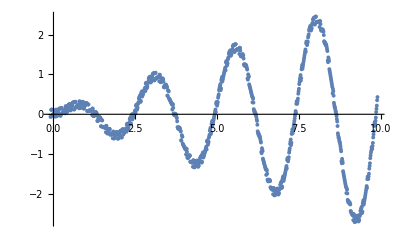

```mathematica
WykresDane=ListPlot[Dane]
```

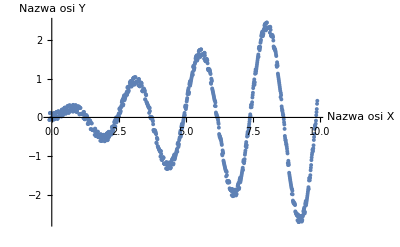

```mathematica
Show[WykresDane,AxesLabel->{HoldForm[Nazwa osi X],HoldForm[Nazwa osi Y]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
nlm=NonlinearModelFit[Dane, a*x*Sin[b*x+c]+d,{a,b,c,d},x]
```

FittedModel[0.0360626-0.29296 x Sin[12.573-2.55094 x]]

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.29296 | 0.00052144 | 561.829 | 1.7758469869×10^-1248
b | 2.55094 | 0.000896797 | 2844.5 | 2.08335096419×10^-1949
c | -12.573 | 0.00692377 | -1815.91 | 2.5807894887×10^-1755
d | 0.0360626 | 0.00207517 | 17.3781 | 2.75755×10^-59

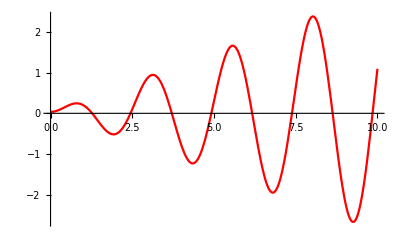

```mathematica
WykresFitu=Plot[nlm["BestFit"],{x,0,10}, PlotStyle->Red]
```

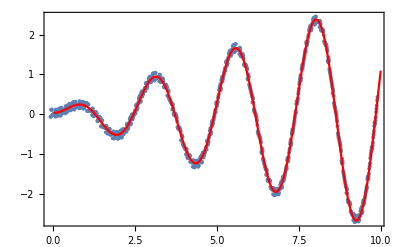

```mathematica
Show[WykresDane,WykresFitu,Frame->True,Axes->None]
```

```mathematica
Export["z3_wyniki_fitu.dat",Transpose[{nlm["BestFitParameters"][[All,2]],nlm["ParameterErrors"]}],"Table"]
```

```mathematica
"z3_wyniki_fitu.dat"
```

```mathematica
Zadanie 2
```

```mathematica
NoweDaneY=1/(3+Dane[[All,2]])
```

{0.340841,0.340003,0.321524,0.321026,0.320523,0.336665,0.335832,0.334999,0.334167,1/3,0.3325,0.331666,0.330831,0.329996,0.329161,0.340248,0.321524,0.320808,0.325814,0.338727,0.337602,0.336485,0.328752,0.327783,0.326817,0.319949,0.319113,0.318277,0.318591,0.317735,0.337846,0.336542,0.318,0.317095,0.316193,0.331445,0.330202,0.328971,0.327754,0.326549,0.325358,0.324181,0.323017,0.321867,0.320732,0.330899,0.31286,0.311892,0.316336,0.328201,0.326868,0.325559,0.318079,0.316953,0.315846,0.309246,0.308299,0.30737,0.308079,0.30715,0.311475,0.322997,0.32174,0.320512,0.313307,0.312267,0.311253,0.304906,0.304057,0.303232,0.30347,0.302668,0.320859,0.319704,0.302967,0.302207,0.301473,0.315424,0.314439,0.313487,0.312567,0.311682,0.310828,0.310008,0.30922,0.308465,0.307742,0.317453,0.301164,0.300636,0.305166,0.31665,0.315886,0.31516,0.308644,0.308099,0.307588,0.30186,0.302039,0.30171,0.306481,0.318295,0.317753,0.31725,0.310871,0.310543,0.310249,0.304639,0.304501,0.304393,0.305371,0.305306,0.324683,0.324366,0.30794,0.307953,0.307997,0.323469,0.323336,0.323237,0.323173,0.323142,0.323146,0.323182,0.323251,0.323351,0.323483,0.335226,0.318005,0.31831,0.324313,0.338312,0.338431,0.338585,0.332014,0.332318,0.332648,0.32684,0.327302,0.327788,0.330157,0.330665,0.337326,0.35268,0.352985,0.353314,0.346313,0.346779,0.347264,0.34105,0.341653,0.342271,0.344242,0.34487,0.370586,0.370927,0.350242,0.350869,0.351504,0.372412,0.372806,0.373207,0.373612,0.374022,0.374434,0.374846,0.375257,0.375666,0.37607,0.392231,0.368985,0.369473,0.377616,0.396709,0.396797,0.396873,0.387693,0.387868,0.388023,0.379806,0.380042,0.380251,0.401653,0.401485,0.401291,0.401068,0.400814,0.400529,0.400211,0.399859,0.417263,0.390229,0.389923,0.398091,0.41833,0.417362,0.416361,0.405216,0.404333,0.403408,0.393473,0.392647,0.391776,0.393501,0.392488,0.400029,0.419648,0.417854,0.416025,0.404114,0.40245,0.40075,0.390197,0.388635,0.387037,0.387096,0.385385,0.414805,0.412225,0.384165,0.382221,0.380248,0.401732,0.399076,0.396407,0.393729,0.391042,0.388348,0.385649,0.382947,0.380241,0.377535,0.39045,0.364443,0.361967,0.366728,0.381381,0.378169,0.374983,0.3637,0.360813,0.357946,0.348096,0.345484,0.342888,0.364611,0.361286,0.338403,0.335783,0.333189,0.348421,0.345315,0.342254,0.339237,0.336266,0.333339,0.330458,0.327624,0.324835,0.322091,0.330667,0.31116,0.30873,0.311578,0.321476,0.318616,0.315818,0.307303,0.304802,0.302352,0.294943,0.292749,0.290599,0.289442,0.287354,0.302196,0.29969,0.283607,0.281634,0.279707,0.290289,0.288091,0.285952,0.283872,0.281847,0.279881,0.277969,0.276113,0.274311,0.272562,0.278931,0.265179,0.263696,0.26609,0.273644,0.271965,0.270343,0.26451,0.263111,0.261763,0.256679,0.255524,0.254417,0.254461,0.253417,0.255966,0.263317,0.262135,0.261009,0.255941,0.255009,0.254127,0.24971,0.249002,0.248337,0.248416,0.247827,0.259866,0.259114,0.248045,0.247598,0.247197,0.25663,0.256137,0.255694,0.255303,0.25496,0.254666,0.254422,0.254227,0.25408,0.253981,0.261005,0.250327,0.250426,0.254066,0.262544,0.262615,0.262739,0.258829,0.259108,0.259437,0.256047,0.256904,0.25742,0.261691,0.271145,0.271671,0.272251,0.268487,0.269217,0.269999,0.266741,0.267665,0.268639,0.270492,0.271562,0.288067,0.28913,0.277232,0.278496,0.279815,0.29396,0.295314,0.296725,0.298195,0.299723,0.301311,0.302958,0.304663,0.306427,0.308251,0.320751,0.306655,0.308672,0.316139,0.331435,0.333591,0.335809,0.331364,0.333712,0.33612,0.332215,0.334745,0.337331,0.341969,0.344667,0.354175,0.373647,0.37652,0.379449,0.373846,0.376871,0.379945,0.374931,0.378089,0.381291,0.386218,0.389499,0.425554,0.42894,0.404088,0.407496,0.410927,0.442727,0.446211,0.449701,0.453192,0.456679,0.460155,0.463613,0.46705,0.470458,0.47383,0.502765,0.467712,0.470963,0.486824,0.52185,0.524747,0.527546,0.513875,0.516524,0.519054,0.506498,0.508867,0.511101,0.552569,0.554167,0.555586,0.556821,0.557861,0.5587,0.559337,0.559763,0.595571,0.542756,0.542803,0.5593,0.600536,0.598827,0.59688,0.574185,0.57221,0.570008,0.549901,0.547681,0.54525,0.547714,0.544742,0.55817,0.595593,0.590315,0.584888,0.559832,0.55476,0.549553,0.527947,0.523062,0.518062,0.515964,0.51066,0.560768,0.553146,0.501281,0.495447,0.489575,0.522753,0.515222,0.507738,0.500305,0.492934,0.485628,0.478398,0.471242,0.464173,0.457191,0.473039,0.432642,0.42643,0.430226,0.447425,0.439957,0.432651,0.414907,0.408408,0.402044,0.387135,0.381429,0.375835,0.39932,0.392633,0.363422,0.35812,0.352939,0.367642,0.361813,0.356146,0.350635,0.345278,0.340069,0.335007,0.330086,0.325305,0.320659,0.327184,0.306349,0.302316,0.303361,0.310972,0.306588,0.302342,0.292984,0.289214,0.285559,0.277583,0.274321,0.271158,0.268909,0.265904,0.277271,0.273913,0.259312,0.256595,0.253965,0.261583,0.25876,0.256035,0.253406,0.250868,0.248421,0.24606,0.243785,0.241593,0.239481,0.243623,0.232392,0.230607,0.231802,0.236874,0.235004,0.233212,0.228321,0.226769,0.225284,0.221063,0.219786,0.21857,0.218228,0.217109,0.218641,0.223653,0.222494,0.221402,0.217495,0.216596,0.215755,0.212386,0.211717,0.211103,0.211046,0.210527,0.219073,0.218482,0.210527,0.210194,0.209914,0.216709,0.21641,0.216169,0.215984,0.215855,0.215783,0.215766,0.215806,0.215901,0.216052,0.221368,0.213898,0.214249,0.217214,0.223728,0.224149,0.224632,0.222171,0.222803,0.223496,0.221436,0.22256,0.223455,0.227209,0.234904,0.235925,0.237016,0.234816,0.23606,0.237373,0.23557,0.237035,0.238571,0.240836,0.242517,0.256545,0.258369,0.249759,0.251749,0.253821,0.26652,0.26878,0.271132,0.273579,0.276122,0.278764,0.281507,0.284352,0.287303,0.290361,0.303023,0.291903,0.295264,0.303721,0.319628,0.323497,0.327501,0.325166,0.329375,0.333723,0.331853,0.336413,0.341116,0.348033,0.35306,0.365426,0.388881,0.394753,0.400806,0.397328,0.403585,0.410023,0.407039,0.41368,0.420504,0.429592,0.436817,0.486554,0.494951,0.465621,0.473691,0.481944,0.530586,0.539992,0.549586,0.559362,0.569314,0.579425,0.589689,0.600092,0.61062,0.621253,0.677686,0.620178,0.630604,0.66443,0.737474,0.749311,0.761047,0.738378,0.749271,0.759953,0.738165,0.747943,0.757409,0.857817,0.867122,0.875848,0.883923,0.891297,0.897924,0.903759,0.908744,1.01139,0.870853,0.873546,0.91954,1.03923,1.03629,1.03214,0.967165,0.962186,0.95616,0.900706,0.894198,0.886824,0.892077,0.882613,0.916296,1.01859,0.99984,0.980633,0.908628,0.891568,0.874225,0.817027,0.801488,0.785799,0.776808,0.760607,0.871475,0.847343,0.726892,0.710162,0.693659,0.756613,0.735456,0.714924,0.695024,0.675749,0.657091,0.639047,0.621604,0.604752,0.588481,0.610072,0.540549,0.527045,0.52891,0.550776,0.5353,0.520481,0.49135,0.478735,0.466612,0.44353,0.433045,0.422946,0.449598,0.437951,0.399243,0.390276,0.381644,0.396193,0.38684,0.377879,0.36929,0.361055,0.353157,0.34558,0.338309,0.331328,0.324625,0.329374,0.306585,0.300925,0.300348,0.306133,0.300277,0.294661,0.284334,0.279407,0.274671,0.266049,0.261863,0.257835,0.254692,0.250927,0.259891,0.25585,0.242102,0.238804,0.235631,0.24125,0.237961,0.234803,0.231773,0.228864,0.226074,0.223396,0.220828,0.218365,0.216003,0.21873,0.209066,0.207076,0.207507,0.211026,0.209029,0.207123,0.202804,0.201148,0.199569,0.19587,0.194506,0.193212,0.19262,0.191441,0.192337,0.195915,0.194754,0.193665,0.19044,0.189539,0.1887,0.185944,0.185274,0.184661,0.18449,0.183982,0.190374,0.18984,0.18374,0.183435,0.183186,0.188317,0.188086,0.187913,0.187799,0.187743,0.187745,0.187805,0.187923,0.188099,0.188333,0.192502,0.186976,0.187409,0.189858,0.195026,0.195573,0.196185,0.194562,0.195321,0.196144,0.194859,0.196051,0.197085,0.200367,0.206733,0.207951,0.209245,0.207988,0.209443,0.210978,0.210065,0.211765,0.213549,0.215948,0.217909,0.229864,0.232051,0.225781,0.228134,0.230591,0.241872,0.244612,0.247475,0.250464,0.253583,0.256838,0.260232,0.263772,0.267461,0.271308,0.283653,0.275139,0.279426,0.288385,0.304252,0.309383,0.314735,0.314272,0.319963,0.325896,0.325952,0.332261,0.338839,0.347761,0.354964,0.369835,0.396596,0.40554,0.41489,0.414101,0.42397,0.434278,0.434113,0.444998,0.456371,0.470761,0.483279,0.54981,0.565697,0.532212,0.547498,0.563488,0.637369,0.657527,0.678675,0.700854,0.724113,0.748503,0.774072,0.800871,0.82894,0.858325,0.98228,0.875511,0.906487,0.989746,1.17708,1.22439,1.27376,1.22746,1.2745,1.32303,1.27385,1.31923,1.36539,1.75645,1.82262,1.88882,1.95454,2.01894,2.0813,2.14069,2.19616,2.95561,2.02836,2.0619,2.36027,3.39202,3.39743,3.38455,2.7915,2.76488,2.7265,2.32477,2.28498,2.23819,2.27046,2.20658,2.42307,3.28192,3.0756,2.88027,2.32072,2.19645,2.07775,1.76822,1.6839,1.60313,1.55294,1.47667,1.93731,1.80018,1.31907,1.2532,1.19148,1.37448,1.29172,1.21631,1.14739,1.08428,1.02635,0.973056,0.923933,0.878565,0.836589,0.871916,0.730066,0.699565,0.696675,0.72821,0.69497,0.664209,0.612306,0.587969,0.565208,0.52764,0.509041,0.491519,0.4789,0.462993,0.45927,0.470296,0.454005,0.438708,0.413786,0.401046,0.38901,0.369719,0.359498,0.356644,0.362683,0.352424,0.342722,0.326985,0.318701,0.31083,0.298223,0.291413}

```mathematica
OX=Table[q,{q,0,49.95,0.05}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.,5.05,5.1,5.15,5.2,5.25,5.3,5.35,5.4,5.45,5.5,5.55,5.6,5.65,5.7,5.75,5.8,5.85,5.9,5.95,6.,6.05,6.1,6.15,6.2,6.25,6.3,6.35,6.4,6.45,6.5,6.55,6.6,6.65,6.7,6.75,6.8,6.85,6.9,6.95,7.,7.05,7.1,7.15,7.2,7.25,7.3,7.35,7.4,7.45,7.5,7.55,7.6,7.65,7.7,7.75,7.8,7.85,7.9,7.95,8.,8.05,8.1,8.15,8.2,8.25,8.3,8.35,8.4,8.45,8.5,8.55,8.6,8.65,8.7,8.75,8.8,8.85,8.9,8.95,9.,9.05,9.1,9.15,9.2,9.25,9.3,9.35,9.4,9.45,9.5,9.55,9.6,9.65,9.7,9.75,9.8,9.85,9.9,9.95,10.,10.05,10.1,10.15,10.2,10.25,10.3,10.35,10.4,10.45,10.5,10.55,10.6,10.65,10.7,10.75,10.8,10.85,10.9,10.95,11.,11.05,11.1,11.15,11.2,11.25,11.3,11.35,11.4,11.45,11.5,11.55,11.6,11.65,11.7,11.75,11.8,11.85,11.9,11.95,12.,12.05,12.1,12.15,12.2,12.25,12.3,12.35,12.4,12.45,12.5,12.55,12.6,12.65,12.7,12.75,12.8,12.85,12.9,12.95,13.,13.05,13.1,13.15,13.2,13.25,13.3,13.35,13.4,13.45,13.5,13.55,13.6,13.65,13.7,13.75,13.8,13.85,13.9,13.95,14.,14.05,14.1,14.15,14.2,14.25,14.3,14.35,14.4,14.45,14.5,14.55,14.6,14.65,14.7,14.75,14.8,14.85,14.9,14.95,15.,15.05,15.1,15.15,15.2,15.25,15.3,15.35,15.4,15.45,15.5,15.55,15.6,15.65,15.7,15.75,15.8,15.85,15.9,15.95,16.,16.05,16.1,16.15,16.2,16.25,16.3,16.35,16.4,16.45,16.5,16.55,16.6,16.65,16.7,16.75,16.8,16.85,16.9,16.95,17.,17.05,17.1,17.15,17.2,17.25,17.3,17.35,17.4,17.45,17.5,17.55,17.6,17.65,17.7,17.75,17.8,17.85,17.9,17.95,18.,18.05,18.1,18.15,18.2,18.25,18.3,18.35,18.4,18.45,18.5,18.55,18.6,18.65,18.7,18.75,18.8,18.85,18.9,18.95,19.,19.05,19.1,19.15,19.2,19.25,19.3,19.35,19.4,19.45,19.5,19.55,19.6,19.65,19.7,19.75,19.8,19.85,19.9,19.95,20.,20.05,20.1,20.15,20.2,20.25,20.3,20.35,20.4,20.45,20.5,20.55,20.6,20.65,20.7,20.75,20.8,20.85,20.9,20.95,21.,21.05,21.1,21.15,21.2,21.25,21.3,21.35,21.4,21.45,21.5,21.55,21.6,21.65,21.7,21.75,21.8,21.85,21.9,21.95,22.,22.05,22.1,22.15,22.2,22.25,22.3,22.35,22.4,22.45,22.5,22.55,22.6,22.65,22.7,22.75,22.8,22.85,22.9,22.95,23.,23.05,23.1,23.15,23.2,23.25,23.3,23.35,23.4,23.45,23.5,23.55,23.6,23.65,23.7,23.75,23.8,23.85,23.9,23.95,24.,24.05,24.1,24.15,24.2,24.25,24.3,24.35,24.4,24.45,24.5,24.55,24.6,24.65,24.7,24.75,24.8,24.85,24.9,24.95,25.,25.05,25.1,25.15,25.2,25.25,25.3,25.35,25.4,25.45,25.5,25.55,25.6,25.65,25.7,25.75,25.8,25.85,25.9,25.95,26.,26.05,26.1,26.15,26.2,26.25,26.3,26.35,26.4,26.45,26.5,26.55,26.6,26.65,26.7,26.75,26.8,26.85,26.9,26.95,27.,27.05,27.1,27.15,27.2,27.25,27.3,27.35,27.4,27.45,27.5,27.55,27.6,27.65,27.7,27.75,27.8,27.85,27.9,27.95,28.,28.05,28.1,28.15,28.2,28.25,28.3,28.35,28.4,28.45,28.5,28.55,28.6,28.65,28.7,28.75,28.8,28.85,28.9,28.95,29.,29.05,29.1,29.15,29.2,29.25,29.3,29.35,29.4,29.45,29.5,29.55,29.6,29.65,29.7,29.75,29.8,29.85,29.9,29.95,30.,30.05,30.1,30.15,30.2,30.25,30.3,30.35,30.4,30.45,30.5,30.55,30.6,30.65,30.7,30.75,30.8,30.85,30.9,30.95,31.,31.05,31.1,31.15,31.2,31.25,31.3,31.35,31.4,31.45,31.5,31.55,31.6,31.65,31.7,31.75,31.8,31.85,31.9,31.95,32.,32.05,32.1,32.15,32.2,32.25,32.3,32.35,32.4,32.45,32.5,32.55,32.6,32.65,32.7,32.75,32.8,32.85,32.9,32.95,33.,33.05,33.1,33.15,33.2,33.25,33.3,33.35,33.4,33.45,33.5,33.55,33.6,33.65,33.7,33.75,33.8,33.85,33.9,33.95,34.,34.05,34.1,34.15,34.2,34.25,34.3,34.35,34.4,34.45,34.5,34.55,34.6,34.65,34.7,34.75,34.8,34.85,34.9,34.95,35.,35.05,35.1,35.15,35.2,35.25,35.3,35.35,35.4,35.45,35.5,35.55,35.6,35.65,35.7,35.75,35.8,35.85,35.9,35.95,36.,36.05,36.1,36.15,36.2,36.25,36.3,36.35,36.4,36.45,36.5,36.55,36.6,36.65,36.7,36.75,36.8,36.85,36.9,36.95,37.,37.05,37.1,37.15,37.2,37.25,37.3,37.35,37.4,37.45,37.5,37.55,37.6,37.65,37.7,37.75,37.8,37.85,37.9,37.95,38.,38.05,38.1,38.15,38.2,38.25,38.3,38.35,38.4,38.45,38.5,38.55,38.6,38.65,38.7,38.75,38.8,38.85,38.9,38.95,39.,39.05,39.1,39.15,39.2,39.25,39.3,39.35,39.4,39.45,39.5,39.55,39.6,39.65,39.7,39.75,39.8,39.85,39.9,39.95,40.,40.05,40.1,40.15,40.2,40.25,40.3,40.35,40.4,40.45,40.5,40.55,40.6,40.65,40.7,40.75,40.8,40.85,40.9,40.95,41.,41.05,41.1,41.15,41.2,41.25,41.3,41.35,41.4,41.45,41.5,41.55,41.6,41.65,41.7,41.75,41.8,41.85,41.9,41.95,42.,42.05,42.1,42.15,42.2,42.25,42.3,42.35,42.4,42.45,42.5,42.55,42.6,42.65,42.7,42.75,42.8,42.85,42.9,42.95,43.,43.05,43.1,43.15,43.2,43.25,43.3,43.35,43.4,43.45,43.5,43.55,43.6,43.65,43.7,43.75,43.8,43.85,43.9,43.95,44.,44.05,44.1,44.15,44.2,44.25,44.3,44.35,44.4,44.45,44.5,44.55,44.6,44.65,44.7,44.75,44.8,44.85,44.9,44.95,45.,45.05,45.1,45.15,45.2,45.25,45.3,45.35,45.4,45.45,45.5,45.55,45.6,45.65,45.7,45.75,45.8,45.85,45.9,45.95,46.,46.05,46.1,46.15,46.2,46.25,46.3,46.35,46.4,46.45,46.5,46.55,46.6,46.65,46.7,46.75,46.8,46.85,46.9,46.95,47.,47.05,47.1,47.15,47.2,47.25,47.3,47.35,47.4,47.45,47.5,47.55,47.6,47.65,47.7,47.75,47.8,47.85,47.9,47.95,48.,48.05,48.1,48.15,48.2,48.25,48.3,48.35,48.4,48.45,48.5,48.55,48.6,48.65,48.7,48.75,48.8,48.85,48.9,48.95,49.,49.05,49.1,49.15,49.2,49.25,49.3,49.35,49.4,49.45,49.5,49.55,49.6,49.65,49.7,49.75,49.8,49.85,49.9,49.95}

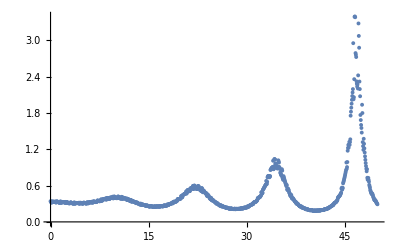

```mathematica
ListPlot[Transpose[{OX,NoweDaneY}],PlotRange->All]
```